```mathematica
(*Mathematica Cookbook*)
```

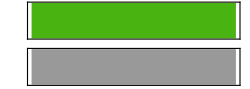

```mathematica
Sound[SoundNote[0,0.125,"GuitarOverdriven",SoundVolume ->1]]
```

```mathematica
(*
带权重的随机选择  
0.125 的选择概率是其他三个数的10 倍  
*)
RandomChoice[{10,1,1,1}->{0.125,0.5,0.75,1.0}]
```

```mathematica
RandomChoice[{5,2,1,3,4,6,2,1}->{"Aflat2","Bflat2","C3","Dflat3","Eflat3","F3","G3","Aflat3"}, 10]
```

{Dflat3,G3,Aflat2,Dflat3,F3,Aflat2,Dflat3,Dflat3,F3,Eflat3}

```mathematica
allPerc= {"BassDrum","BassDrum2","BellTree","Cabasa","Castanets","ChineseCymbal","Clap","Claves","Cowbell","CrashCymbal"}
```

{BassDrum,BassDrum2,BellTree,Cabasa,Castanets,ChineseCymbal,Clap,Claves,Cowbell,CrashCymbal}

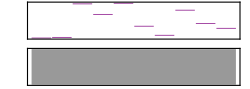

```mathematica
Sound[SoundNote[#, 0.125]& /@ allPerc]
```

```mathematica
(*

Mathematica 提供了60 种打击乐器  
"BassDrum","BassDrum2","BellTree","Cabasa","Castanets","ChineseCymbal","Clap","Claves","Cowbell","CrashCymbal","CrashCymbal2","ElectricSnare","GuiroLong","GuiroShort","HighAgogo","HighBongo","HighCongaMute","HighCongaOpen","HighFloorTom","HighTimbale","HighTom","HighWoodblock","HiHatClosed","HiHatOpen","HiHatPedal","JingleBell","LowAgogo","LowBongo","LowConga","LowFloorTom","LowTimbale","LowTom","LowWoodblock","Maracas","MetronomeBell","MetronomeClick","MidTom","MidTom2","MuteCuica","MuteSurdo","MuteTriangle","OpenCuica","OpenSurdo","OpenTriangle","RideBell","RideCymbal","RideCymbal2","ScratchPull","ScratchPush","Shaker","SideStick","Slap","Snare","SplashCymbal","SquareClick","Sticks","Tambourine","Vibraslap","WhistleLong","WhistleShort"  
*)
```

```mathematica
(*
-Graphics-
 percussion 打击乐器  
 drum kit 架子鼓  
 bass drum 低音大鼓，又称"底鼓"、“贝司鼓”，用底鼓踏板演奏  
 snare drum 军鼓 最核心的部分，手上技巧体现所在      
Hi-Hat Cymbal 脚踏钹bó  

tom tom 中鼓，两个  
 Floor Tom 落地鼓 
  
ride cymbal and crash cymbal 铜钹，两片  
五鼓：底鼓，军鼓，高音桶鼓，中音桶鼓，低音桶鼓  
三镲：吊镲，节奏镲(叮叮镲)，踩镲  

Hi-Hat Cymbal 脚踏钹bó，又称“踩镲chǎ”，“高帽钹bó” 上下两片镲构成，踩镲踏板控制镲片开合，鼓棒敲击镲片进行演奏 
 很可能是音符最为密集的一个声部  
 关闭的时候颗粒感强、音量小，适合较为安静的音乐风格  
 开镲的时候，不但镲片本身会震动，上下两片还会相互碰撞，不但会产生较大音量，延音也较长，适合比较吵闹的风格

强音镲 音色比较炸裂，通常我们会在一首乐曲的开头，转折，结尾时敲击强音镲。主要作用可以是提示、推进情绪、烘托气氛等    

节奏骨架为底鼓、军鼓、踩钗三个最重要的声部位置  
*)
```

```mathematica
(*
bass/bass drum/kick/kick drum/大鼓,底鼓
twin bass/double bass/twin kick/双大鼓
twin pedal/double pedal/双踏板
bass drum beater/踏板上面的敲槌
tom 桶鼓
mountend tom 挂架上的桶鼓
floor tom 地桶
snare/snare drum 军鼓
snare/snappy snare 响弦
hoop/边圈,压圈
rim/边圈
bearing edge 鼓身与鼓皮接触的部分.drumhead/head 鼓皮
batter head/打击面皮
snare head 响弦皮
bottom head/resonant head/桶鼓底鼓的底皮
tension 张力
tone 音高
tune (动词,给鼓调音) tuning (名词,给乐器调音) 这里的调音不是调音台上调音的概念.以下是关于镲片的,国内的翻译十分牵强,但似乎也没有什么确切的词语表达其原意,为统一和理解起见,就硬翻一次:hi-hat 踩镲
crash 碎镲 (这么翻译把crash 一词象声表达的爆发力都埋没了,没办法)
ride 点镲 (因ride一词,有一种"行进"的意味)
splash 水镲 (splash 是短促的溅水声)
china/china crash 中国镲,反镲
bell 镲帽,钟形部位
taper 镲片的主要平面部分
edge 镲片边缘
stick 鼓槌
tip 鼓槌头部
nylon tip 尼龙头,wood tip 木头
neck 鼓槌颈部
butt end 鼓槌尾部
这些更是教材中经常涉及的词汇，关于基本的：pattern：形式，主要是用来分析槌法如何分配用的。比如 the pattern "RLLRRL" could be used in various fills 就是:RLLRRL这个形式可用在各种加花里。sticking:槌法。play 16th notes in different stickings. ：用不同的槌法演奏16分音符(rlrl,rrll,rlrr 等等）。rudiments:基本功
stroke:击
single stroke:单击一次
single stroke roll:单击滚奏，RLRLRLRL........，有时简称为singles
double stroke:双击一次
double stroke roll:双击滚奏，RRLLRRLLRRLLRRLL.........,有时简称doubles
flam:单叠 lR,rL
drag:双叠 llR,rrL
paradiddle和类似的词汇:一个para就是一个交替，一个diddle就是一个"嗒嗒"的双击。所以 paraparadiddle 就是 RLRLRR,LRLRLL.flam-paradiddle-diddle 就是 lRLRRLL,rLRLLRR。均可以此类推。accent:重音 throw in accents in ur paradiddles:在复合跳中加入重音。32nd/16th/8th/quarter/half/whole note:32分/16分/8分/4分/半/全 音符。(英国的说法可能不一样，但不常见，不赘述）
triplet:三连音
***tuplet:六连音
dynamics:强弱
even:平均 常有这句话：make sure that each note/stroke is even.确保每个音符/击打都平均。beat:拍 和我们的习惯一样，一般指4分音符作为一拍。keep time:保持时值。a drummer is to keep time.鼓手的职责就是保持时值。weak/off hand:弱手 train ur off hand.训练你的弱手。lead:起 a left-lead pattern 一个左起的形式。lead with your weak hand.用你的弱手起
*)
```